# 解析几何

## 常见距离定义及等距线形状

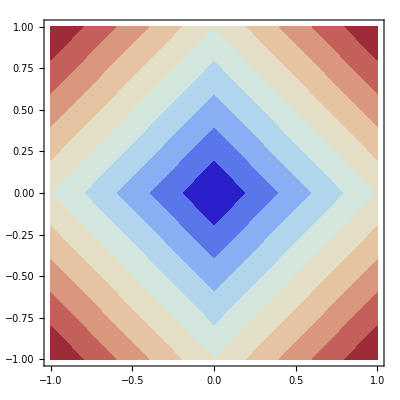
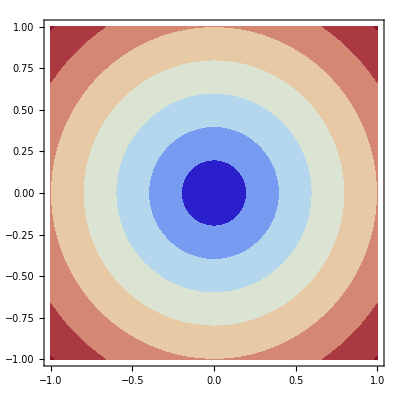
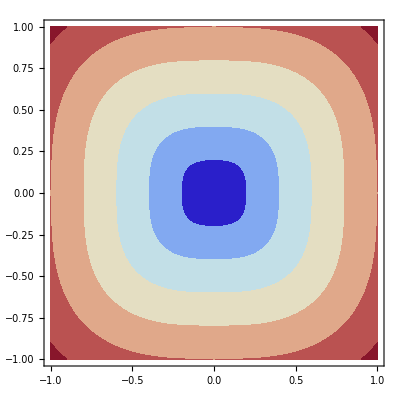
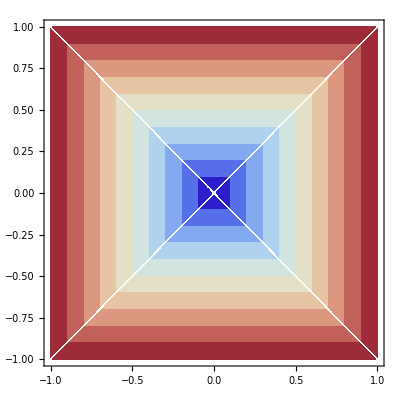

```mathematica
Table[ContourPlot[Norm[{x,y},p],{x,-1,1},{y,-1,1},ContourStyle->None,ColorFunction->"ThermometerColors"],{p,{1,2,3,Infinity}}]
```

## 离心率连续变化条件下一组圆锥曲线

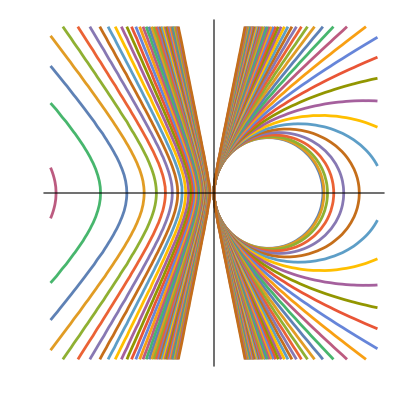

```mathematica
ContourPlot[Evaluate@Table[x2^2==2x1+(e^2-1)x1^2,{e,0,5,0.1}],{x1,-3,3},{x2,-3,3},PlotTheme->"Minimal"] (*p=1*)
```

## 椭圆和双曲线的“叠加”

```mathematica
SuperPositionPlot[m_,n_,{ρ0_,ρ1_}]:=ContourPlot[Evaluate@Table[x1^2/m^2+x2^2/n^2-2ρ x1 x2/(m n)==1,{ρ,ρ0,ρ1,0.1}],{x1,-3,3},{x2,-3,3},PlotTheme->"Minimal"]
```

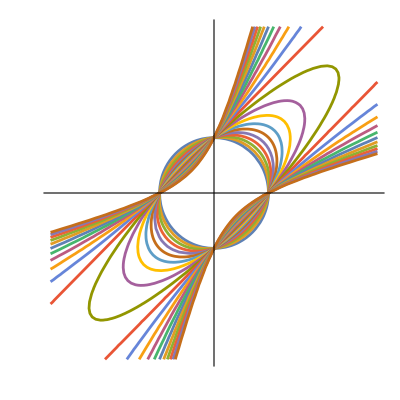
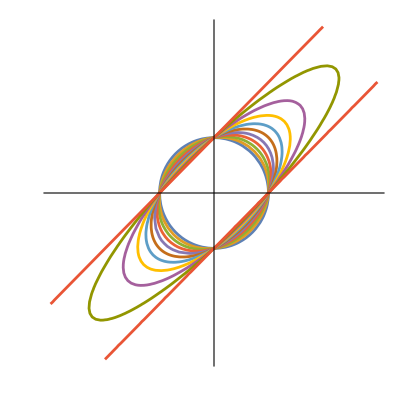

```mathematica
{SuperPositionPlot[1,1,{0,2}],SuperPositionPlot[1,1,{0,1}]}
```

```mathematica
(*{SuperPositionPlot[1,1,{-2,0}],SuperPositionPlot[1,1,{-1,0}]}*)
```

```mathematica
(*{SuperPositionPlot[2,1,{0,2}],SuperPositionPlot[2,1,{-2,0}]}*)
```

## 旋转椭圆

```mathematica
RotatedEllipsePlot[m_,n_,{ρ0_,ρ1_}]:=ContourPlot[Evaluate@Table[x1^2/m^2+x2^2/n^2-2ρ x1 x2/(m n)==1-ρ^2,{ρ,ρ0,ρ1,0.1}],{x1,-m-.5,m+.5},{x2,-n-.5,n+.5},PlotTheme->"Minimal"]
```

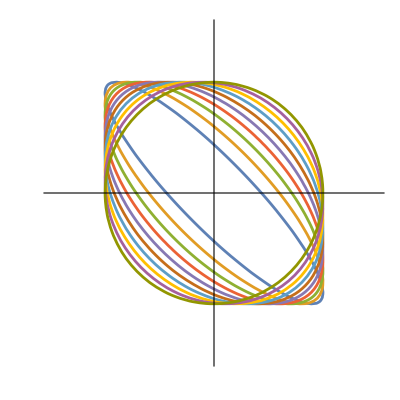
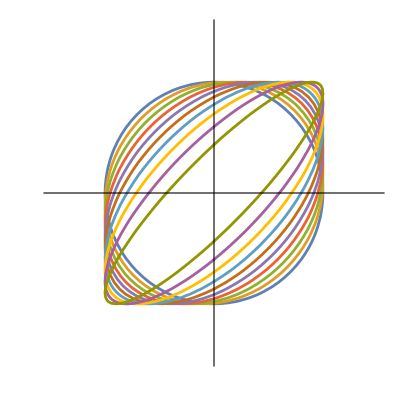
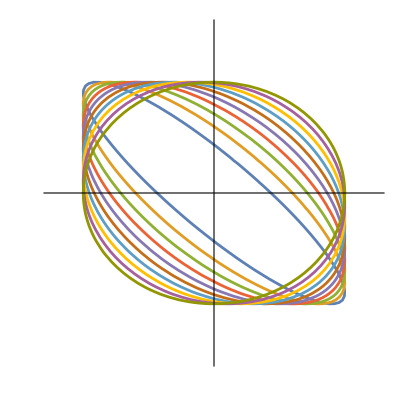
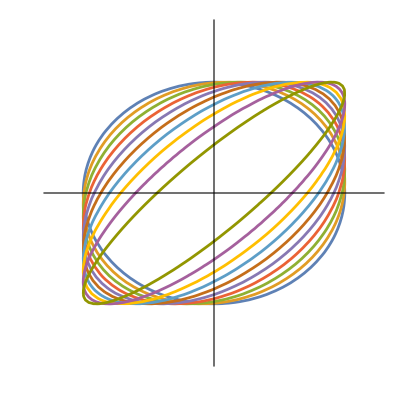
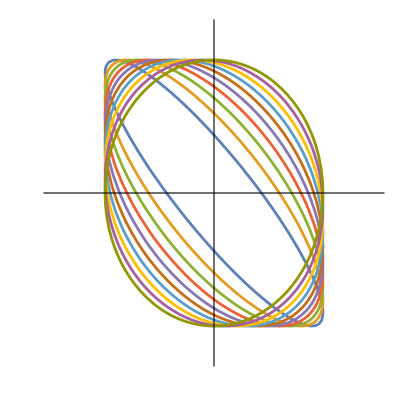
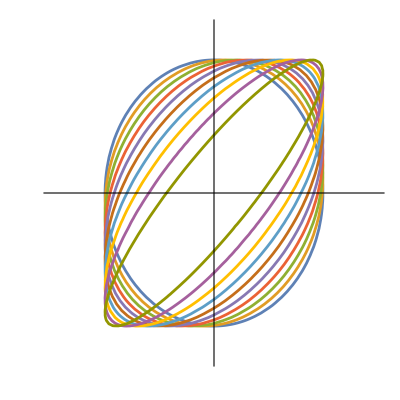

```mathematica
{{RotatedEllipsePlot[1,1,{-.9,0}],RotatedEllipsePlot[1,1,{0,.9}]} (*m=n*),
{RotatedEllipsePlot[2,1,{-.9,0}],RotatedEllipsePlot[2,1,{0,.9}]} (*m>n*),
{RotatedEllipsePlot[1,2,{-.9,0}],RotatedEllipsePlot[1,2,{0,.9}]} (*m<n*)}
```

## 超椭圆

```mathematica
SuperEllipsePlot[a_,b_,p_,q_]:=ContourPlot[Abs[x1/a]^p+Abs[x2/b]^q,{x1,-2,2},{x2,-2,2},PlotRange->All,PlotTheme->"Minimal",Contours->10,ContourStyle->None,ColorFunction->"ThermometerColors"]
```

```mathematica
Table[SuperEllipsePlot[1,1,p,q],{p,{0.5,1,2,3}},{q,{0.5,1,2,3}}];
MapThread[Prepend,{%,{"q=0.5","q=1","q=2","q=3"}}];(*加每行说明*)
Grid@Prepend[%,{" ","p=0.5","p=1","p=2","p=3"}](*加每列说明*)
```

## 超椭球

```mathematica
SuperEllipsoidPlot[a_,b_,c_,t_,r_]:=ContourPlot3D[(Abs[x1/a]^r+Abs[x2/b]^r)^(t/r)+Abs[x3/c]^t==1,{x1,-1.5,1.5},{x2,-1.5,1.5},{x3,-1.5,1.5},PlotTheme->"Scientific",Axes->False]
```

```mathematica
Table[SuperEllipsoidPlot[1,1,1,t,r],{t,{0.8,1,2,3}},{r,{0.8,1,2,3}}];
MapThread[Prepend,{%,{"t=0.8","t=1","t=2","t=3"}}];(*加每行说明*)
Grid@Prepend[%,{" ","r=0.8","r=1","r=2","r=3"}](*加每列说明*)
```